# Integration of various coupled scalar-GB-eqs with radial perturbation

This notebook is aimed to study the stability of BH solutions in quartic-scalar-GB theory under radial perturbations.

```mathematica
Quit[];
```

### Needed files

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Loading the system of equations from auxiliary file*)
perturbEQS=Import["Needed Files/general_perturb_GBeqs.m"]; (*file containing the perturbed equation obtained by the notebook used in article 1903.06784_Gualtieri*)
backEQS=Import["Needed Files/general_background_eqs.m"];
perturbedSCH=Import["Needed Files/Schwarz_perturb_GBeqs.m"]; (*Perturbed equation for Schwarzschild background*)
perturbedSCHϕ0=Import["Needed Files/Schwarz_perturb_GBeqs_generalϕ0value.m"];
```

```mathematica
(*Load packages for numerical integration*)
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["GUIKit`"];
```

#### Importing data

```mathematica
(*Extracts the part of the table corresponding to scalarized solution,giving the corresponding values of η,λ,Subscript[ϕ, h],M,Q*)
```

```mathematica
(*ReadList["Data/etaFund_lambda=0.5η.dat"];
TAB=quarticBranch;
tabelQ={};
tab07Q={};
Do[If[TAB[[i,3]]>0,Massa=( TAB[[i,4]]);tabelQ=AppendTo[tabelQ,{TAB[[i,1]],TAB[[i,2]],TAB[[i,3]],Massa,TAB[[i,5]]*Massa}]],{i,1,Length[TAB]}];
Do[If[tabelQ[[i,1]]<=0.726,(*Print["η=", tabel[[i,1]] ," ","Massa=" ,tabel[[i,3]], " ","Q=", tabel[[i,4]]];*)tab07Q=AppendTo[tab07Q,tabelQ[[i]]]],{i,1,Length[tabelQ]}]
nomefile=StringJoin[{"Data/FundBranch_λ=0.5η.m"}];
Save[nomefile,tab07Q];*)
```

```mathematica
FundExp=ReadList["Data/Branches/Fund_Exponential.dat"][[1]]; (*Fundamental branch of Exponential coupling*)
FundPhi3=ReadList["Data/Branches/Phi3FundBranch.m"][[1]]; (*Fundamental branch with λ=-0.5η meaning it is stable *)
FundQuarticOnly=ReadList["Data/Branches/QuarticFundBranch.m"][[1]]; (*Fundamental branch of quartic only coupling*)
FundTwoThree=ReadList["Data/Branches/FundTwoThree_λ=-η.dat"][[1]];
(*Fundamental branch of polynomial coupling with powers 2 and 3*)
FundExpA3=ReadList["Data/Branches/Fund_Exponential_a=3.dat"][[1]];
```

## Background fields integration

In this case we write the metric ds2 = −A(r)dt^2+ (B(r))^-1 dr^2 + r^2 dΩ^2. 
Now we simplify the background diff equations imposing α=1/2 and that we want a simple theory with no scalar field potential

```mathematica
BEQS=Simplify[backEQS//.{Vf->(0&),α->1/2}];
```

```mathematica
(*Define the coupling function we will study.*)
```

```mathematica
(*ruleCoupling={F-> ((η/8#^2+λ/16#^4)&)};*)
ruleThird={F-> ((η/12#^3)&)};
ruleExponential={F->((η/(4*2a)(1-Exp[-a#^2]))&)};
ruleQuartic={F-> ((η/16#^4)&)};
ruleQuadratic={F-> ((η/8#^2)&)};
ruleTwoThree={F-> ((η/8#^2+λ/12#^3)&)};
ruleTwoFour={F-> ((η/8#^2+λ/16#^4)&)};
```

```mathematica
Rh=1;(*Setting the event horizon value*)
```

### Background Boundary conditions

```mathematica
BCSbckHor=<<"Needed Files/expanded_bck_BCS_hor.m";
```

Boundary condition for the background at the horizon. We shall consider only terms up to second order.

```mathematica
bouhor={Sum[Subscript[ai, i](r-1)^i,{i,1,2}],Sum[Subscript[bi, i](r-1)^i,{i,1,2}],Sum[Subscript[fi, i](r-1)^i,{i,0,2}],D[Sum[Subscript[fi, i](r-1)^i,{i,0,2}],r]};
```

### Background Integration

I’ll work with compactified coordinate x=1-rh/r so that the event horizon is mapped at x->0 and r->∞ is at x->1

```mathematica
(*CBEQ are the background equations in compactified coordinates*)
```

```mathematica
CBEQ=(1-x)^3 BEQS/.{A->(A[1-Rh/#]&),B->(B[1-Rh/#]&),ϕ->(ϕ[1-Rh/#]&)}/.r->Rh/(1-x)//Simplify;
```

```mathematica
Clear[CsGBINT];
```

CsGBINT:   (rh, ϕh, η, λ, rmax, Nh, ruleCoupling, ) ->  (ϕinf, ϕ[r],ϕ'[r],A[r],A'[r],B[r],B'[r],ϕ0,Q/M, η/M^2,λ/M^2,M )   Integration of the equations for a given choice of rh, ϕh, η, λ

```mathematica
CsGBINT[phic0_,coupConst_,xmax0_,xinf_,MODEL_,ϵ0_]:=(
rh0=1;
(*Parameters to be used in the integrator*)
rulePARAM={MaxSteps->Infinity,PrecisionGoal->13,AccuracyGoal->13,InterpolationOrder->All,Method->"StiffnessSwitching"};
(*ϵ0 difines how far from the horizon we will start our integrations*)

(*Initial conditions*)
(*Georgios' way*)
BChorrule=BCSbckHor//.MODEL;
ruBChor=BChorrule//.coupConst/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0/.rh->rh0;

BOU=Thread[{A[x],B[x],ϕ[x],(-1+x)^2 ϕ'[x]}==(bouhor//.ruBChor/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0/.rh->rh0/.r->1/(1-x))]/.x->ϵ0;

BCS=BOU;
(*Numerical integration*)
sol=NDSolve[
Union[Union[{CBEQ[[2]]==0,CBEQ[[1]]==0, CBEQ[[3]]==0}//.MODEL/.coupConst],BCS],
{A,B,ϕ},
{x,ϵ0,xmax0},
rulePARAM][[1]];

(* Solutions of the numerical integration.
Observe that Λ, which is the radial metric function that appears in the spheric simmetric metric, can be obtained from ϕ and Υ according to 
 Eqs. (A1) and (A2) from Kanti+, here generalized*)
ϕsol=ϕ[x]/.sol;
Dϕsol=D[ϕsol,x];
Asol=A[x]/.sol;
DAsol=D[Asol,x];
Bsol=B[x]/.sol;
DBsol=D[Bsol,x];
(*Values of variables at infinity*)
ϕinf=ϕsol/.{x-> xmax0};
Ainf=Asol/.{x-> xmax0};
Binf=Bsol/.{x-> xmax0};
Asolshift=Asol/Ainf;


PhysicalParams=NSolve[{
Asolshift==1-(2 M)/r+((M Q^2)/(12 r^3)),
ϕsol==ϕ0+Q/r+(M Q)/r^2+((32 M^2 Q-Q^3)/(24 r^3)),
((1-x)^2/rh0)D[ϕsol,x]==D[ϕ0+Q/r+(M Q)/r^2,r]&&M≥ 0 }/.r->rh0/(1-x)/.{x->xinf},{ϕ0,Q,M}][[1]];

(*Output: ϕinf, ϕsol, Dϕsol, A[r], A'[r], B[r], B'[r], ϕ0, Q/M, M*)
{ϕinf,
ϕsol,
Dϕsol,
Asol*(Binf/Ainf),
DAsol*(Binf/Ainf),
Bsol(*/Binf*),
DBsol(*/Binf*),
ϕ0/.PhysicalParams,
(Q/M)/.PhysicalParams,
M/.PhysicalParams
}
);
```

I also report the integration in radial coordinate which is useful then for the effective potential study and to have the constant Wronskian for the perturbed eq. solutions

```mathematica
sGBINT[phic0_,coupConst_,rmax0_,NHorizons0_,MODEL_,ϵ0_]:=(
rh0=1;
(*Parameters to be used in the integrator*)
rulePARAM={MaxSteps->Infinity,PrecisionGoal->13,AccuracyGoal->13,InterpolationOrder->All,Method->"StiffnessSwitching"};
(*Initial conditions*)
(*Georgios' way*)
BChorrule=BCSbckHor//.MODEL;
ruBChor=BChorrule//.coupConst/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0/.rh->rh0;

BOUr=Thread[{A[r],B[r],ϕ[r],ϕ'[r]}==(bouhor//.ruBChor/.Subscript[fi, 0]->phic0/.Subscript[ai, 1]->rh0/.rh->rh0)]/.r->rh0+ϵ0;

BCSr={
A[r]==N[r-rh],
B[r]==N[r-rh],
ϕ'[r]==N[(rh/(4 F'[ϕ[r]]))(-1+Sqrt[1-96 ((F'[ϕ[r]])^2/rh^4)])]//.Union[MODEL,{η->η0, λ->λ0}],
(*condizione necessaria affinché ϕ'' non diverga all'orizzonte.*)
ϕ[r]==phic0
}/.coupConst//.{r->rh0+ϵ0,rh-> rh0,ϕ[rh]->phic0};

BCSr=BOUr;
(*Numerical integration*)
solr=NDSolve[
Union[Union[{BEQS[[2]]==0,BEQS[[1]]==0, BEQS[[3]]==0}//.MODEL/.coupConst],BCSr],
{A,B,ϕ},
{r,rh0+ϵ0,rmax0},
rulePARAM][[1]];

(* Solutions of the numerical integration.
Observe that Λ, which is the radial metric function that appears in the spheric simmetric metric, can be obtained from ϕ and Υ according to 
 Eqs. (A1) and (A2) from Kanti+, here generalized*)
ϕsolr=ϕ[r]/.solr;
Dϕsolr=D[ϕsolr,r];
Asolr=A[r]/.solr;
DAsolr=D[Asolr,r];
Bsolr=B[r]/.solr;
DBsolr=D[Bsolr,r];
(*Values of variables at infinity*)
ϕinfr=ϕsolr/.{r-> rmax0};
Ainfr=Asolr/.{r-> rmax0};
Binfr=Bsolr/.{r-> rmax0};
Asolshiftr=Asolr/Ainfr;

(*Extract physical parameters of the BH solution*)
PhysicalParams=NSolve[{
Asolshiftr==1-(2 Mr)/r+((Mr *Qr^2)/(12 r^3)),
ϕsolr==ϕ0r+Qr/r+(Mr* Qr)/r^2+((32 Mr^2 Qr-Qr^3)/(24 r^3)),
D[ϕsolr,r]==D[ϕ0r+Qr/r+(Mr* Qr)/r^2,r]&&Mr≥ 0 }/.{r->rh0*NHorizons0},{ϕ0r,Qr,Mr}][[1]];

(*NOTA: entrambe le costanti di accoppiamento η e λ hanno (dimensione [length])^2, mentre il campo scalare à adimensionale in tale trattazione e lo scalare di Gauss-Bonnet (è [length])^-4*)
(*Nell'output restituisco l'esponenziale delle funzioni metriche Υ e Λ, che chiamo A[r] e B[r]*)

(*Output: ϕ0, ϕinf, Q/M, M, ϕsol, Dϕsol, A[r], A'[r], B[r], B'[r]*)
{ϕ0r/.PhysicalParams,
ϕinfr,
(Qr/Mr)/.PhysicalParams,
Mr/.PhysicalParams,
ϕsolr,
Dϕsolr,
Asolr/Ainfr,
DAsolr/Ainfr,
Bsolr(*/Binf*),
DBsolr(*/Binf*)
}
);
```

## Perturbed integration

### Perturbed equations

I’m interested in the simplest case where the potential Vf = 0. Moreover the perturbEQS has a constant value α which can be set to 1/2 for the whole analysis: in fact it varies depending on the metric used for the background field integration, i.e.  if the metric functions are defined as exp(Υ) or exp(2Υ), etc.

The equation we need is the following: - ∂^2 φ1/∂r^2  + h(r) ∂^2 φ1/∂t^2 + k(r)∂φ1/∂r +p(r)φ1=0. In perturbEQS we have this equation but in a more general form, so we have to simplify it a little for our problem.

```mathematica
(*Salcedo's equations*)
```

```mathematica
PEQS=Simplify[perturbEQS//.{Vf[ϕ[r]]->0, Vf'[ϕ[r]]->0,Vf''[ϕ[r]]->0,α->1/2}];
```

```mathematica
PEQSom=PEQS/.ϕ1->(φ[#2]Exp[-I ω #1]&)/.t->0//Simplify;
```

```mathematica
CPEQS=PEQSom/.{A->(A[1-1/#]&),B->(B[1-1/#]&),ϕ->(ϕ[1-1/#]&),φ->(φ[1-1/#]&)}/.r->Rh/(1-x)//Simplify;
(*toNorm=Coefficient[CPEQS,φ''[x]];
CPEQS2=CPEQS/toNorm//Simplify;*)
```

```mathematica
(*for the Schwarzschild background*)
```

```mathematica
CPEQsch=perturbedSCH/.Vf->(0&)/.α->1/2/.ϕ1->((φ[#2]Exp[-I ω #1])&)/.t->0/.φ->(φ[1-1/#]&)/.r->1/(1-x)//Simplify
```

1/(-1+x)^6(-(-1+x)^4 x (1-288 (-1+x)^5 F'[0]^2-336 (-1+x)^6 F'[0]^2) φ'[x]+(1-x)^3 φ[x] (x-288 (-1+x)^5 F'[0]^2-528 (-1+x)^6 F'[0]^2-240 (-1+x)^7 F'[0]^2+12 (-1+x)^3 F''[0]+12 (-1+x)^4 F''[0])-(1-48 (-1+x)^6 F'[0]^2) (ω^2 φ[x]+(-1+x)^3 x^2 (2 φ'[x]+(-1+x) φ''[x])))

```mathematica
CPEQschϕ0=perturbedSCHϕ0/.Vf->(0&)/.α->1/2/.ϕ1->((φ[#2]Exp[-I ω #1])&)/.t->0/.φ->(φ[1-1/#]&)/.r->1/(1-x)/.ϕ0->ϕz//Simplify
```

1/(-1+x)^6(-(-1+x)^4 x (1-48 (-1+x)^5 (-1+7 x) F'[ϕz]^2) φ'[x]+(1-x)^3 x φ[x] (1-48 (-1+x)^5 (1+5 x) F'[ϕz]^2+12 (-1+x)^3 F''[ϕz])-(1-48 (-1+x)^6 F'[ϕz]^2) (ω^2 φ[x]+(-1+x)^3 x^2 (2 φ'[x]+(-1+x) φ''[x])))

```mathematica
(*
(CPEQschϕ0/.ruleCoupling/.ϕz->0)==CPEQsch/.ruleCoupling//Simplify*)
```

((-(-1+x)^4 x (1-48 (-1+x)^5 (-1+7 x) F'[0]^2) φ'[x]+(1-x)^3 x φ[x] (1-48 (-1+x)^5 (1+5 x) F'[0]^2+12 (-1+x)^3 F''[0])-(1-48 (-1+x)^6 F'[0]^2) (ω^2 φ[x]+(-1+x)^3 x^2 (2 φ'[x]+(-1+x) φ''[x])))/(-1+x)^6/.ruleCoupling)==1/(-1+x)^6(-(-1+x)^4 x (1-288 (-1+x)^5 F'[0]^2-336 (-1+x)^6 F'[0]^2) φ'[x]+(1-x)^3 φ[x] (x-288 (-1+x)^5 F'[0]^2-528 (-1+x)^6 F'[0]^2-240 (-1+x)^7 F'[0]^2+12 (-1+x)^3 F''[0]+12 (-1+x)^4 F''[0])-(1-48 (-1+x)^6 F'[0]^2) (ω^2 φ[x]+(-1+x)^3 x^2 (2 φ'[x]+(-1+x) φ''[x])))/.ruleCoupling

### Integration functions

#### Schwarzschild BH background

```mathematica
ϕ0Finding[MODEL_]:=(
Clear[couple];
couple[ϕz_]:=F[ϕz]/.MODEL;
SchSol=Solve[{couple'[ϕz]==0,ϕz!=0},ϕz];
SchSol
);
```

INPUT:  rh, {coupling constants}, coupling function,  ω_i,  xmiddle,  distance from horizon in x
OUTPUT:   φ^(-), Dφ^(-),  φ^(+), Dφ^(+)

```mathematica
PINTEGschϕ0[coupConst_,MODEL_,ω0_,xm_ ,ϵ0_,choosesol_]:=(
rh0=1;
(*Parameters to be used in the integrator.*)
rulePAR={MaxSteps->Infinity,(*PrecisionGoal->10,*)AccuracyGoal->20,InterpolationOrder->All(*MaxStepSize->0.01*),Method->"StiffnessSwitching"};

(*ϵ0 tells how far from the horizon we will start our integrations*)
xmin=ϵ0;
xinf=0.99;
(*these are the values of the derivative of the field perturbation φ respectively at the horizon and at infinity*)
cminus=1;
cplus=-1;

(*we choose which solution of the equation F'[ϕ]=0 to take: if choosesol=0 -> ϕh=0 else ϕh=ϕ0Finding*)
If[choosesol==0, phi0=(ϕz->0),phi0=ϕ0Finding[MODEL][[1]]];

CPEQschw=CPEQschϕ0/.MODEL/.phi0;

(*Writing the analytical expression for φ using the Schwarzschild tortoise coordinate*)
tortSch[x_]:=rh0/(1-x)+rh0 Log[x/(1-x)];

PBCSminSCH={
φ[x]==N[Exp[ω0 *tortSch[x]]],
φ'[x]==N[D[Exp[ω0 *tortSch[x]],x]]}//.{x->xmin};

(*Boundary conditions for the integration towards infinity*)
PBCSplusSCH={
φ[x]==0(*φSCH//.x->xmax*),
φ'[x]==cons(*DφSCH/.x->xmax*)
}//.{x->xinf, cons->cplus};

(*Numerical integration. SOLminus is the solution for the integration around x=0; SOLplus around x->1*)
SOLminusSCH=NDSolve[Union[{CPEQschw==0//.{ω^2->- ω0^2,rh->rh0}/.coupConst},PBCSminSCH],φ,
{x,xmin,xm+ϵ0},
rulePAR];
SOLplusSCH=NDSolve[Union[{CPEQschw==0//.{ω^2->- ω0^2,rh->rh0}/.coupConst},PBCSplusSCH],φ,
{x,xinf,xm-ϵ0},
rulePAR];

(*Solutions: φminus=φ^(-),Dφminus=φ^(-)', φplus=φ^(+), Dφplus=φ^(-)'*)
φminusSCH=φ[x]/.SOLminusSCH;
DφminusSCH=D[φminusSCH,x];
φplusSCH=φ[x]/.SOLplusSCH;
DφplusSCH=D[φplusSCH,x];

(*Output: φ^(-), Dφ^(-), φ^(+), Dφ^(+)*)
{φminusSCH(*/(φminusSCH/.x->xm)*),
DφminusSCH(*/(φminusSCH/.x->xm)*),
φplusSCH(*/(φplusSCH/.x->xm)*),
DφplusSCH(*/(φplusSCH/.x->xm)*)}

);
```

INPUT:  rh, {coupling constants}, coupling function,  ω_i,  xmiddle,  distance from horizon in x
OUTPUT:   φ^(-), Dφ^(-),  φ^(+), Dφ^(+)

```mathematica
PINTEGsch[coupConst_,MODEL_,ω0_,xm_ ,ϵ0_]:=(
rh0=1;
(*Parameters to be used in the integrator.*)
rulePAR={MaxSteps->Infinity,(*PrecisionGoal->10,*)AccuracyGoal->20,InterpolationOrder->All(*MaxStepSize->0.01*),Method->"StiffnessSwitching"};

(*ϵ0 tells how far from the horizon we will start our integrations*)
xmin=ϵ0;
xinf=0.99;
(*these are the values of the derivative of the field perturbation φ respectively at the horizon and at infinity*)
cminus=1;
cplus=-1;

(*Boundary conditions: we want the perturbation to be outgoing at infinity and ingoing at the horizon. These requests lead to the following conditions.*)

CPEQschw=CPEQsch/.MODEL;

(*Writing the analytical expression for φ using the Schwarzschild tortoise coordinate*)
tortSch[x_]:=rh0/(1-x)+rh0 Log[x/(1-x)];

PBCSminSCH={
φ[x]==N[Exp[ω0 *tortSch[x]]],
φ'[x]==N[D[Exp[ω0 *tortSch[x]],x]]}//.{x->xmin};

(*Boundary conditions for the integration towards infinity*)
PBCSplusSCH={
φ[x]==0(*φSCH//.x->xmax*),
φ'[x]==cons(*DφSCH/.x->xmax*)
}//.{x->xinf, cons->cplus};

(*Numerical integration. SOLminus is the solution for the integration around x=0; SOLplus around x->1*)
SOLminusSCH=NDSolve[Union[{CPEQschw==0//.{ω^2->- ω0^2,rh->rh0}/.coupConst},PBCSminSCH],φ,
{x,xmin,xm+ϵ0},
rulePAR];
SOLplusSCH=NDSolve[Union[{CPEQschw==0//.{ω^2->- ω0^2,rh->rh0}/.coupConst},PBCSplusSCH],φ,
{x,xinf,xm-ϵ0},
rulePAR];

(*Solutions: φminus=φ^(-),Dφminus=φ^(-)', φplus=φ^(+), Dφplus=φ^(-)'*)
φminusSCH=φ[x]/.SOLminusSCH;
DφminusSCH=D[φminusSCH,x];
φplusSCH=φ[x]/.SOLplusSCH;
DφplusSCH=D[φplusSCH,x];

(*Output: φ^(-), Dφ^(-), φ^(+), Dφ^(+)*)
{φminusSCH(*/(φminusSCH/.x->xm)*),
DφminusSCH(*/(φminusSCH/.x->xm)*),
φplusSCH(*/(φplusSCH/.x->xm)*),
DφplusSCH(*/(φplusSCH/.x->xm)*)}

);
```

#### Scalarized BH solutions

INPUT:  rh,  ϕh,  η,  λ,  rmax[r],  Nhorizons,  ruleCoupling,  ω_i,  xmiddle,  distance from horizon in x
OUTPUT:   φ^(-), Dφ^(-),  φ^(+), Dφ^(+)

note:  rh is always set to 1; rmax is given in r and it’s used for the CsGBINT, same as Nhorizons;  ωi is the Imaginary part of the frequency (Real number)

```mathematica
PINTEGx[phic0_,coupConst_,rmax0_,NHorizons0_,MODEL_, ω0_,xm_,xmin_,xmax_,precision_ ]:=(
rh0=1;
(*Parameters to be used in the integrator.*)
rulePAR={MaxSteps->Infinity,PrecisionGoal->precision,AccuracyGoal->precision,InterpolationOrder->All(*MaxStepSize->0.01*),Method->"StiffnessSwitching"};
ϵ0=xmin;
ϵ2=10^-15;(*How far from the horizon we will start our integrations*)
(*xmin=ϵ0;*)
(*xmax=0.99;*)
(*these are the values of the derivative of the field perturbation φ respectively at the horizon and at infinity*)
cminus=1;
cplus=1;

(*Defining the background metric functions AA[r], BB[r] and the background field Φ[t,r]
We rewrite input and output of the sGBINT to remember
Input: ϕh,couplingConstants,rmax,Nh,rule
	output: ϕ0, Φinf, Q/M, M, Φsol, DΦsol, A[r], A'[r], B[r], B'[r]*)

BCKGRNDr=sGBINT[phic0,coupConst,rmax0,NHorizons0,MODEL,ϵ2];
BCKGRND=CsGBINT[phic0,coupConst,1-1/rmax0,1-1/NHorizons0,MODEL,xmin];
AA=BCKGRND[[4]];
BB=BCKGRND[[6]];
ϕbck=BCKGRND[[2]];

ruleCOEFF={A[x]->AA, A'[x]->D[AA,x],A''[x]->D[D[AA,x],x],B[x]->BB,B'[x]->D[BB,x],B''[x]->D[D[BB,x],x],ϕ[x]->ϕbck,ϕ'[x]->D[ϕbck,x],ϕ''[x]->D[D[ϕbck,x],x]};

(*CPEQ is the perturbed diff eq depending on x, the one we will integrate*)
CPEQ=CPEQS/.MODEL/.coupConst/.rh->rh0/.(*sol*)ruleCOEFF;

PEQ=PEQSom/.MODEL/.coupConst/.{rh->rh0}/.solr;

(*Writing the analytical expression for φ using the Schwarzschild tortoise coordinate as first approximation*)
tortSch[x_]:=rh0/(1-x)+rh0 Log[x/(1-x)];

PBCSmin={
φ[x]==N[Exp[ω0 *tortSch[x]]],
φ'[x]==N[D[Exp[ω0 *tortSch[x]],x]]}//.{x->xmin};


(*Boundary conditions for the integration towards infinity*)
PBCSplus={
φ[x]==0(*/.x->xmax*),
φ'[x]==cons(*/.x->xmax*)
}//.{x->xmax, cons->cplus};

(*Numerical integration. SOLminus is the solution for the integration around x=0; SOLplus around x->1*)
SOLminus=NDSolve[Union[{CPEQ==0//.{ω^2->- ω0^2,rh->rh0}},PBCSmin(*us*)],φ,
{x,xmin,xm(*+0.3*)+ϵ0},
rulePAR];
SOLplus=NDSolve[Union[{CPEQ==0//.{ω^2->- ω0^2,rh->rh0}},PBCSplus],φ,
{x,xmax,xm(*-0.3*)-ϵ0},
rulePAR];

(*Solutions: φminus=φ^(-),Dφminus=φ^(-)', φplus=φ^(+), Dφplus=φ^(-)'*)
φminus=φ[x]/.SOLminus;
Dφminus=D[φminus,x];
φplus=φ[x]/.SOLplus;
Dφplus=D[φplus,x];

(*Output: φ^(-), Dφ^(-), φ^(+), Dφ^(+)*)
{φminus/(φminus/.x->xm),
Dφminus/(φminus/.x->xm),
φplus/(φplus/.x->xm),
Dφplus/(φplus/.x->xm)}

);
```

```mathematica
numero=1;
xm=0.5;
tab=FundExp;
ruleCoupling=ruleExponential;
eta=tab[[numero,1]];
cou={η->eta,a->3/2};
phih=tab[[numero,2]];
outx=PINTEGx[phih,cou,10^12,150,ruleCoupling,0.09,xm,10^-8];
phiminDx=outx[[1]];
phipluDx=outx[[3]];
DphiminDx=outx[[2]];
DphipluDx=outx[[4]];
(phiminDx/DphiminDx-phipluDx/DphipluDx)/.x->xm
```

{2.37167}

Up to xmax =0.99 time becomes unsostainable, same for smax=0.97 and precision 10. Let’s find the best compromise

```mathematica
{1.0503425805056117}(*10^-8, precision=8, xmax=0.97, tempo 18 sec*)
```

```mathematica
{1.038984930490566}(*10^-8, precision=8, xmax=0.95, tempo 1.5 sec*)
```

```mathematica
{1.0484916967879538}(*10^-8, precision=8, xmax=0.98, tempo 195 sec*)
```

```mathematica
{1.0389847320561802}(*10^-8, precision=10, xmax=0.95, tempo 50 sec*)
```

```mathematica
{1.0389847073736247}(*10^-8, precision=9, xmax=0.95, tempo 6 sec*)
```

```mathematica
{1.0389714167296917} (*10^-10, precision=9, xmax=0.95, tempo 9 sec*)
```

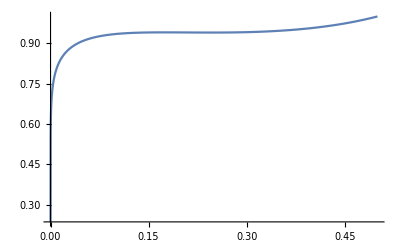

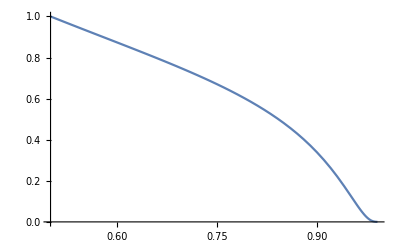

```mathematica
Plot[phiminDx,{x,xmin,xm}, PlotRange->Full]
Plot[phipluDx,{x,xm,xmax}]
```

```mathematica
tab[[1]]
```

{23.2037,0.251372,0.50668,0.0744205}

```mathematica
BCKGRND
```

{-1.53632×10^-6,InterpolatingFunction[…][x],InterpolatingFunction[…][x],0.706297 InterpolatingFunction[…][x],0.706297 InterpolatingFunction[…][x],InterpolatingFunction[…][x],InterpolatingFunction[…][x],-1.55898×10^-6,0.14687,0.50668}

```mathematica
(*GraphicsRow[{Plot[phiminDx,{x,xmin,xm},PlotRange->Full,PlotLabel->Style[Framed["φ^(-)"],16,Blue]],
Plot[DphiminDx,{x,xmin,xm},PlotRange->Automatic,PlotLabel->Style[Framed["Dφ^(-)"],16,Blue]]}]
GraphicsRow[{Plot[phipluDx,{x,xm,xmax},PlotRange->Full,PlotLabel->Style[Framed["φ^(+)"],16,Red]],
Plot[DphipluDx,{x,xm,xmax},PlotRange->Full,PlotLabel->Style[Framed["Dφ^(+)"],16,Red]]}]
(*Plot[φSCH,{x,xmax,xinf},PlotRange->Full]*)
phiminDx/DphiminDx-phipluDx/DphipluDx/.x->0.5*)
```

### Tortoise coordinate and Effective potential

I want to compute the solution in the tortoise coordinate R defined as dR/dr=g, where g is the square root of the coefficient of the perturbed differential equation written in this way:
g^2 (∂^2 φ)/(∂t^2)-(∂^2 φ)/(∂r^2)+C (∂φ)/(∂r)+Uφ=0, so in our case (g^2) =-Hr/Nr. In this way I can write the differential equation in this form (-d^2/dR^2+ Veff)Z=ω^2Z and so that the Wronskian computed with respect to the tortoise coordinate is constant. Z is such that φ=F * Z and F satisfies the equation (2F')/F=C-g'/g with all this functions dependent on r

```mathematica
(*numero=1;
xm=0.5;
tab=FundInsta;
eta=tab[[numero,1]];
lambda=tab[[numero,2]];
phih=tab[[numero,3]];
outx=PINTEGx[Rh,phih,eta,lambda,10^12,150,ruleCoupling,0.09,xm,10^-8];
phimin=outx[[1]];
phiplus=outx[[3]];
Dphimin=outx[[2]];
Dphiplus=outx[[4]];*)
```

```mathematica
(*GraphicsRow[{Plot[phimin,{x,2*10^-16,xm+0.3}],Plot[phiplus,{x,xm-0.3,0.99}]}]*)
```

```mathematica
(*coefome=Coefficient[PEQ,ω^2];*)
```

```mathematica
(*PEQ2=PEQ/.ω->0(*//Simplify*);*)
```

```mathematica
(*PEQ2==PEQ-coefome*ω^2;*)
```

```mathematica
(*coef=Coefficient[PEQ2,{φ[r],φ'[r],φ''[r]}];
coefC=coef[[2]];(*k*)
coef1=coef[[3]];(*n*)
coefU=coef[[1]];(*p*)
coefg=Coefficient[coefome,φ[r]];(*-h: lui è -h perché derivando 2 volte rispetto al tempo porto giù un (-I)^2 e h era preso invece prima di derivare*)*)
```

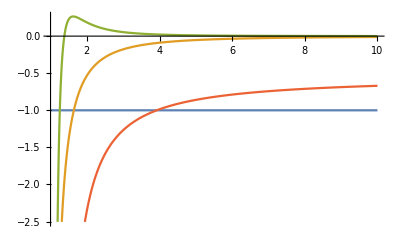

```mathematica
(*Plot[{-coef1/coef1,-coefC/coef1,-coefU/coef1,-coefg/coef1},{r,1,10}]*)
```

```mathematica
(*(*Defining coefficients functions as in Doneva's paper*)
g[rr_]:=Sqrt[(coefg/coef1)]/.r->rr//Simplify;
c[rr_]:=-coefC/coef1/.r->rr//Simplify;
u[rr_]:=-coefU/coef1/.r->rr//Simplify;
*)
```

```mathematica
(**)
```

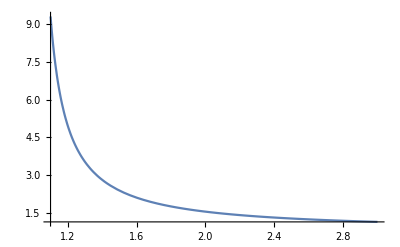

```mathematica
(*Plot[g[rr],{rr,1.1,3},PlotRange->Full]*)
```

```mathematica
(*(*this is the differential equation that the function ff[r] (difined by φ[r]=ff[r]Z[r]) must satisfy*)
Clear[eqtortoise];
eqtortoise[rr_]:=(2fun'[rr]/fun[rr]-c[rr]+g'[rr]/g[rr]);*)
```

```mathematica
(*(*integration*)
BCfun=fun[Rh+10^-6]==1;
SOLfun=NDSolve[{eqtortoise[rr]==0,BCfun},fun,{rr,1+10^-5,20},rulePAR][[1]];
ff[rr_]:=fun[rr]/.SOLfun;
*)
```

```mathematica
(*Plot[{ff[rr]},{rr,Rh+10^-2,3},PlotRange->Full]*)
```

```mathematica
(*DChange[x_]:=(1-x)^2/Rh;*)
```

```mathematica
(*(*Passing again to r coordinate for the solutions that are computed in the compactified coordinate x*)
phiminr[rr_]:=phimin/.x->{1-Rh/rr};
Dphiminr[rr_]:=DChange[x]^-1*Dphimin/.x->{1-Rh/rr};
phiplur[rr_]:=phiplus/.x->{1-Rh/rr};
Dphiplur[rr_]:=DChange[x]^-1*Dphiplus/.x->{1-Rh/rr};*)
```

```mathematica
(*
(*Computing the Z^(-) and Z^(+) functions according to φ[r]=ff[r]Z[r]*)
Zmin[rr_]:=phiminr[rr]/ff[rr];
Zplus[rr_]:=phiplur[rr]/ff[rr];

(*Finally I can compute the Wronskian in tortoise coordinate, whose value doesn't depend on the matching point*)
WRO[rm_]:=g[rm]^-1(Zmin[rm]*Zplus'[rm]-Zplus[rm]*Zmin'[rm])(*/(ff[rm]^2 Zmin'[rm]*Zplus'[rm]+ff'[rm]*Zmin[rm]Zplus[rm])*);*)
```

```mathematica
(*Table[WRO[i][[1]],{i,2,5}]*)
```

```mathematica
(*Table[WROGG[i][[1]],{i,2,5}]*)
```

```mathematica
(*Plot[{WRO[rm],WROGG[rm]},{rm,1.25,5},PlotRange->{-10^-16,10^-9}]*)
```

```mathematica
(*Veff[rr_]:=g[rr]^-2 (u[rr]-ff''[rr]/ff[rr]-c[rr]/ff[rr] ff'[rr]);
CVeff[x_]:=Veff[rr]/.rr->Rh/(1-x);*)
```

```mathematica
(*Veff[5]*)
```

```mathematica
(*Plot[{Veff[rr],VeffG[rr]},{rr,1.0001,3}, PlotRange->Full]*)
```

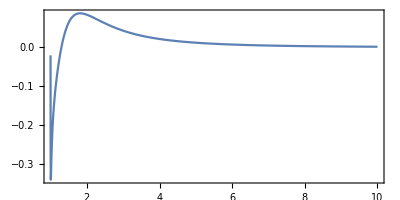
-Graphics-r/r_hV_effr_h^2

```mathematica
(*Labeled[GraphicsRow[{Plot[Veff[rr],{rr,1.0001,10}, PlotRange->Full,Frame->True,AspectRatio->1/2,LabelStyle->Directive[Black,Medium]](*,Plot[CVeff[x],{x,0.1,0.9}, PlotRange->Full]*)}],{"r/r_h","V_effr_h^2"},{Bottom,Left}]*)
```

```mathematica
WRO[5]
```

## Shooting method with Wronskian

Here we search for the eigenvalue ωi corresponding to the frequency at which the Wronskian W = [φ^(-)(dφ^(+)/dx)- (dφ^(-)/dx) φ^(+)]_(x=x_m) vanishes

### Schwarzschild BH

```mathematica
WRONSKsch[η0_,λ0_, ω0_, xm_,ϵ0_]:=(
(*Finding φ^(-) and φ^(+) with the PINTEG function*)
out=PINTEGsch[1,η0,λ0,ruleCoupling,ω0,xm,ϵ0];
phimin=out[[1]];
phiplu=out[[3]];
Dphimin=out[[2]];
Dphiplu=out[[4]];

Wrons1=((phimin/Dphimin-phiplu/Dphiplu)/.x->xm)[[1]]; (*Georgios definition*)
Wrons2=((phimin*Dphiplu-phiplu*Dphimin)/.x->xm)[[1]]; (*Canonic definition*)

(*product of the derivatives at the matching point*)
prod=((Dphimin*Dphiplu)/.x->xm)[[1]];

{Wrons1,
Wrons2,
prod}
);
WRONSKschϕ0[η0_,λ0_, ω0_, xm_,ϵ0_,choosesol_]:=(
(*Finding φ^(-) and φ^(+) with the PINTEG function*)
out=PINTEGschϕ0[1,η0,λ0,ruleCoupling,ω0,xm,ϵ0,choosesol];
phimin=out[[1]];
phiplu=out[[3]];
Dphimin=out[[2]];
Dphiplu=out[[4]];

Wrons1=((phimin/Dphimin-phiplu/Dphiplu)/.x->xm)[[1]]; (*Georgios definition*)
Wrons2=((phimin*Dphiplu-phiplu*Dphimin)/.x->xm)[[1]]; (*Canonic definition*)

(*product of the derivatives at the matching point*)
prod=((Dphimin*Dphiplu)/.x->xm)[[1]];

{Wrons1,
Wrons2,
prod}
);
```

Here in green there is the routine that computes the Wronskian for different values of ωi for every coupling parameters value and for Sch. Background.
I checked the last value of η at which we have scalarized solution up to the forth decimal place is ηi=0.7256

```mathematica
(*
xmiddle=0.5;
(*shooting method to find the eigenvalue ωi*)
pts=800;

wi=0.8;
wf=3;
step=(wf-wi)/pts;

ηi=0.7256;
ηf=3;
λmultiplier=-1.5;
epts=25;
omeshoot[z_]:=wi+(z-1)/pts(wf-wi);
etap[z_]:=ηi+(ηf-ηi)/epts(z-1);
(*tab=SchwBckSol;*)
choosesoln=1;

xnear=2*10^-16;
minimaSch={};
Monitor[
Table[
(*Clear[{PINTEGx,WRONSK,ωshoot}];*)
WROGsch[k]={};
ηk=etap[k];
λk=λmultiplier*ηk;
Monitor[
Do[{
ωshoot=omeshoot[j];
check=WRONSKschϕ0[ηk,λk,ωshoot,xmiddle,xnear,choosesoln](*[[1,1]]*);
WROGsch[k]=AppendTo[WROGsch[k],{ωshoot,check[[1]]}]},{j,1,pts}],j];
min=Min[Table[WROGsch[k][[j,2]]//Abs,{j,1,pts}]];
pos=Position[WROGsch[k]//Abs,min][[1,1]];
omegaok=WROGsch[k][[pos,1]];
minimaSch=AppendTo[minimaSch,{ηk,omegaok}]
,{k,1,epts}]
,k];*)
```

```mathematica
(*check*)
```

WRONSKsch[2.904,4.356,0.79925,0.5,1/5000000000000000,1]

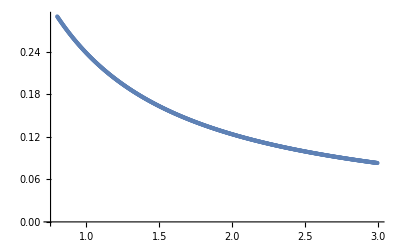
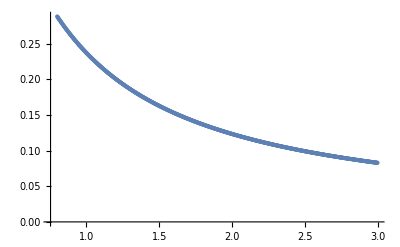
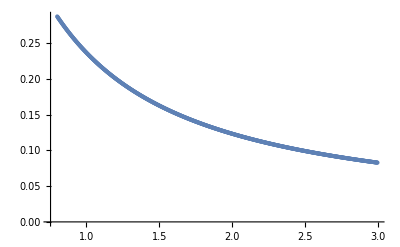
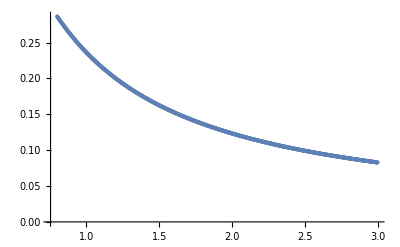
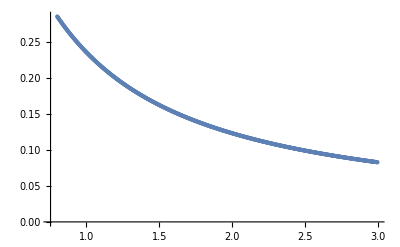
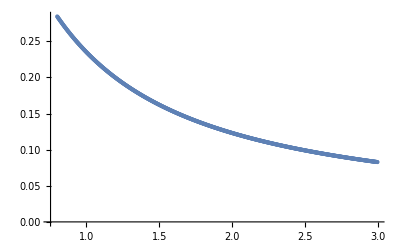
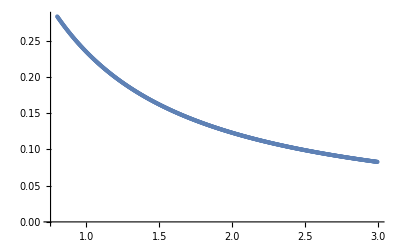
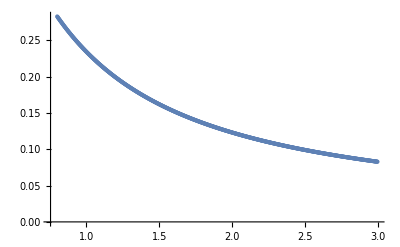

```mathematica
(*Table[ListPlot[WROGsch[i]],{i,1,epts}]*)
```

### Scalarized BH

```mathematica
WRONSK[phih0_,coupConst_,MODEL_, ω0_, xm_,xmin_,xmax_,precision_]:=(
(*Finding φ^(-) and φ^(+) with the PINTEG function*)
out=PINTEGx[phih0,coupConst,10^12,150,MODEL,ω0,xm,xmin,xmax,precision];
phimin=out[[1]];
phiplu=out[[3]];
Dphimin=out[[2]];
Dphiplu=out[[4]];

Wrons1=(((phimin/Dphimin-phiplu/Dphiplu)*Dphimin*Dphiplu)/.x->xm)[[1]]; (*Georgios definition*)
(*Wrons2=((phimin*Dphiplu-phiplu*Dphimin)/.x->xm)[[1]]; (*Canonic definition*)

(*product of the derivatives at the matching point*)
prod=((Dphimin*Dphiplu)/.x->xm)[[1]];
*)
{Wrons1(*,
Wrons2,
prod*)}
);
```

```mathematica
numero=1;
eta=tab[[numero,1]]
phih=tab[[numero,2]]
check2ew=WRONSK[phih,eta,0,ruleCoupling,0.09,0.5,10^-8]
```

2.64745

0.37953

$Aborted

```mathematica
(*{-0.007071011619694367}*)
```

Here in orange there is the routine that computes the Wronskian for different values of ωi for every coupling parameters value

```mathematica
Length[FundExp]
```

7159

```mathematica
Length[FundExpA3]
```

1424

```mathematica
si=1400;
FundExpA3[[si,4]]/FundExp[[si,1]]^(1/2)
FundExpA3[[si,3]]^2/FundExp[[si,1]]
```

1.05074

1.14557

```mathematica
FundInsta[[115]]
```

{0.7,0.35,0.284513,0.507274,0.123126}

#### Exponential coupling

```mathematica
(*xmmin=xmed[[Position[Wxmed,Min[Wxmed]][[1]]]]*)
xmiddle=0.5;
(*shooting method to find the eigenvalue ωi*)
pts=100;

wi=2.5;
wf=3.2;
step=(wf-wi)/pts;
omeshoot[z_]:=wi+(z-1)/pts(wf-wi);
tab=FundExpA3;
ruleCoupling=ruleExponential;

xnear=10^-8;
xmax=0.98;
precision=10;

a0=3; (*coefficient of ϕ^2 term at the exponent*)

minima={};

Monitor[
Table[
(*Clear[{PINTEGx,WRONSK,ωshoot}];*)
WROND[k]={};
ηk=tab[[k,1]];
(*λk=tab[[k,2]];*)
couple={η->ηk,a->a0};
phihk=tab[[k,2]];

Monitor[
Do[{
ωshoot=omeshoot[j];
check=WRONSK[phihk,couple,ruleCoupling,ωshoot,xmiddle,xnear,xmax,precision](*[[1,1]]*);
WROND[k]=AppendTo[WROND[k],{ωshoot,check[[1]]}]}
,{j,1,pts}],j];
min=Min[Table[WROND[k][[j,2]]//Abs,{j,1,pts}]];
pos=Position[WROND[k]//Abs,min][[1,1]];
omegaok=WROND[k][[pos,1]];
minima=AppendTo[minima,{tab[[k,1]],omegaok, tab[[k,3]],tab[[k,4]]}]
,{k,1400,Length[tab]}]
,k];
```

```mathematica
minima={};
Do[min=Min[Table[WRON[k][[j,2]]//Abs,{j,1,90}]];
pos=Position[WRON[k]//Abs,min][[1,1]];
omegaok=WRON[k][[pos,1]];
minima=AppendTo[minima,{tab[[k,1]],omegaok, tab[[k,3]],tab[[k,4]]}],{k,6900,6901}]
```

```mathematica
minima
```

{{84.,2.903,1.05214,1.64463},{85.,2.89,1.05381,1.64353}}

```mathematica
MsuEta=minima[[All,3]]/minima[[All,1]]^(1/2)
ωiM2sueta=minima[[All,2]]*minima[[All,3]]^2/minima[[All,1]]^(1/2)
```

{0.114798,0.114302}

{0.350633,0.348107}

```mathematica
WROND[6900]
```

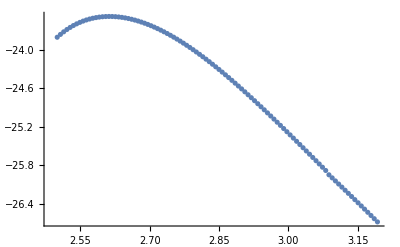

```mathematica
ListPlot[WROND[1421]]
```

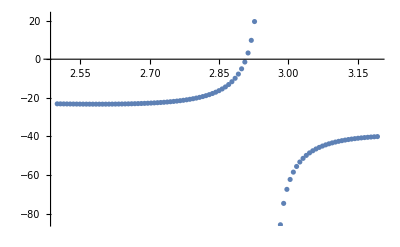

```mathematica
ListPlot[WROND[6900]]
```

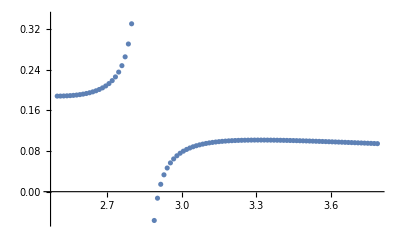

```mathematica
ListPlot[WRON[6900]]
```

```mathematica
nomefile=StringJoin[{"Data/Stability/ExponentialA3_firsttryunstable.dat"}];
Save[nomefile,WROND]
```

#### Polynomial coupling

```mathematica
(*xmmin=xmed[[Position[Wxmed,Min[Wxmed]][[1]]]]*)
xmiddle=0.5;
(*shooting method to find the eigenvalue ωi*)
pts=100;

wi=2;
wf=8;
step=(wf-wi)/pts;
omeshoot[z_]:=wi+(z-1)/pts(wf-wi);
tab=FundTwoThree;
ruleCoupling=ruleTwoThree;

xnear=10^-8;
xmax=0.99;
precision=10;

minima={};

Monitor[
Table[
(*Clear[{PINTEGx,WRONSK,ωshoot}];*)
WRON[k]={};
ηk=tab[[k,1]];
λk=tab[[k,2]];
couple={η->ηk,λ->λk};
phihk=tab[[k,3]];

Monitor[
Do[{
ωshoot=omeshoot[j];
check=WRONSK[phihk,couple,ruleCoupling,ωshoot,xmiddle,xnear,xmax,precision](*[[1,1]]*);
WRON[k]=AppendTo[WRON[k],{ωshoot,check[[1]]}]}
,{j,1,pts}],j];
min=Min[Table[WRON[k][[j,2]]//Abs,{j,1,pts}]];
pos=Position[WRON[k]//Abs,min][[1,1]];
omegaok=WRON[k][[pos,1]];
minima=AppendTo[minima,{tab[[k,1]],tab[[k,2]],omegaok, tab[[k,4]],tab[[k,5]]}]
,{k,102,Length[tab]}]
,k];
```

## Graphics

```mathematica
Clear[minimaSch]
```

Importing file for the fundamental branch

```mathematica
ReadList["Data/Stability/Stability_λ=-0.5η.dat"];
ReadList["../Stability/Data/Control/SchwInstability_newBCS.m"];
```

```mathematica
StabBranch05OmeM=Table[{minima[[i,1]]/(2*minima[[i,4]])^2,-2minima[[i,4]]*minima[[i,3]]},{i,1,Length[minima]}];
SchwUnst15OmeM=Table[{minSch15[[i,1]],-minSch15[[i,2]]},{i,1,Length[minSch15]}];
```

```mathematica
SchwUnst00OmeM=Table[{minimaSch[[i,1]],-minimaSch[[i,2]]},{i,1,Length[minimaSch]}];
```

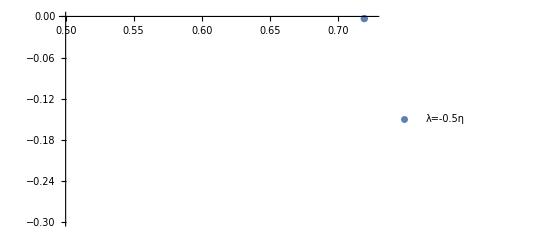
-Graphics--2Mω_iη/(2M)^2

```mathematica
Labeled[ListPlot[Legended[StabBranch05OmeM,"λ=-0.5η"],PlotRange->{{0.5,0.7256},{-0.3,0}}],{"-2Mω_i","η/(2M)^2"},{Left,Top}]
```

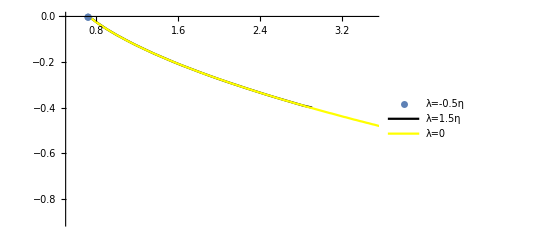
-Graphics--2Mω_iη/(2M)^2

```mathematica
Labeled[Show[ListPlot[Legended[StabBranch05OmeM,"λ=-0.5η"],PlotRange->{{0.5,3.5},{-0.9,0}}],ListLinePlot[Legended[SchwUnst15OmeM,"λ=1.5η"],PlotRange->{{0.5,3.5},{-0.9,0}},PlotStyle->Black],ListLinePlot[Legended[SchwUnst00OmeM,"λ=0"],PlotRange->{{0.5,3.5},{-0.9,0}},PlotStyle->Yellow]],{"-2Mω_i","η/(2M)^2"},{Left,Top}]
```

```mathematica
minimaSch
```

{{0.7303,0.000026251},{0.73045,0.0000912509},{0.7306,0.000156251},{0.73075,0.000221251},{0.7309,0.000286251},{0.73105,0.000351251},{0.7312,0.000415001},{0.73135,0.000480001},{0.7315,0.000545},{0.73165,0.00060875},{0.7318,0.00067375},{0.73195,0.0007375},{0.732072,0.000634975},{0.7321,0.00080125},{0.73225,0.000865},{0.7324,0.00093},{0.73255,0.00099375},{0.7327,0.00099875},{0.73285,0.00099875},{0.738443,0.00344736},{0.744815,0.00594726},{0.751186,0.00844716},{0.757558,0.0106346},{0.763929,0.0131345},{0.770301,0.0153219},{0.776672,0.0175093},{0.783044,0.0193842},{0.789415,0.0215716},{0.795787,0.0237591},{0.802158,0.025634},{0.80853,0.0278214},{0.814901,0.0296963},{0.821273,0.0315712},{0.827644,0.0337587},{0.834016,0.0356336},{0.840387,0.0375085},{0.846759,0.0393834},{0.85313,0.0412584},{0.859502,0.0431333},{0.865873,0.0450082},{0.872245,0.0468831},{0.878616,0.0487581},{0.884988,0.050633},{0.891359,0.0521954},{0.897731,0.0540703},{0.904102,0.0559453},{0.910474,0.0575077},{0.916845,0.0593826},{0.923217,0.0612576},{0.929588,0.06282},{0.93596,0.0646949},{0.942331,0.0662573},{0.948703,0.0681323},{0.955074,0.0696947},{0.961446,0.0712571},{0.967817,0.0731321},{0.974189,0.0746945},{0.98056,0.0762569},{0.986932,0.0781319},{0.993303,0.0796943},{0.999675,0.0812567},{1.00605,0.0828192},{1.01242,0.0843816},{1.01879,0.0859441},{1.02516,0.0875065},{1.03153,0.0893814},{1.0379,0.0909439},{1.04428,0.0925063},{1.05065,0.0940687},{1.05702,0.0956312},{1.06339,0.0968811},{1.06976,0.0984436},{1.07613,0.100006},{1.0825,0.101568},{1.08888,0.103131},{1.09525,0.104693},{1.10162,0.106256},{1.10799,0.107506},{1.11436,0.109068},{1.12073,0.110631},{1.1271,0.111881},{1.13348,0.113443},{1.13985,0.115005},{1.14622,0.116255},{1.15259,0.117818},{1.15896,0.11938},{1.16533,0.12063},{1.17171,0.122193},{1.17808,0.123443},{1.18445,0.125005},{1.19082,0.126255},{1.19719,0.127817},{1.20356,0.129067},{1.20993,0.13063},{1.21631,0.13188},{1.22268,0.133442},{1.22905,0.134692},{1.23542,0.136255},{1.24179,0.137505},{1.24816,0.138754},{1.25453,0.140317},{1.26091,0.141567},{1.26728,0.142817},{1.27365,0.144379},{1.28002,0.145629},{1.28639,0.146879},{1.29276,0.148129},{1.29914,0.149692},{1.30551,0.150941},{1.31188,0.152191},{1.31825,0.153441},{1.32462,0.154691},{1.33099,0.156254},{1.33736,0.157504},{1.34374,0.158754},{1.35011,0.160004},{1.35648,0.161254},{1.36285,0.162504},{1.36922,0.163753},{1.37559,0.165003},{1.38196,0.166253},{1.38834,0.167503},{1.39471,0.168753},{1.40108,0.170003},{1.40745,0.171253},{1.41382,0.172503},{1.42019,0.173753},{1.42657,0.175003},{1.43294,0.176253},{1.43931,0.177503},{1.44568,0.178753},{1.45205,0.180003},{1.45842,0.181253},{1.46479,0.182503},{1.47117,0.183753},{1.47754,0.185003},{1.48391,0.186253},{1.49028,0.18719},{1.49665,0.18844},{1.50302,0.18969},{1.50939,0.19094},{1.51577,0.19219},{1.52214,0.19344},{1.52851,0.194377},{1.53488,0.195627},{1.54125,0.196877},{1.54762,0.198127},{1.554,0.199065},{1.56037,0.200314},{1.56674,0.201564},{1.57311,0.202814},{1.57948,0.203752},{1.58585,0.205002},{1.59222,0.206252},{1.5986,0.207189},{1.60497,0.208439},{1.61134,0.209689},{1.61771,0.210627},{1.62408,0.211877},{1.63045,0.213126},{1.63682,0.214064},{1.6432,0.215314},{1.64957,0.216251},{1.65594,0.217501},{1.66231,0.218751},{1.66868,0.219689},{1.67505,0.220939},{1.68143,0.221876},{1.6878,0.223126},{1.69417,0.224064},{1.70054,0.225313},{1.70691,0.226251},{1.71328,0.227501},{1.71965,0.228438},{1.72603,0.229688},{1.7324,0.230626},{1.73877,0.231876},{1.74514,0.232813},{1.75151,0.234063},{1.75788,0.235001},{1.76425,0.236251},{1.77063,0.237188},{1.777,0.238438},{1.78337,0.239375},{1.78974,0.240625},{1.79611,0.241563},{1.80248,0.2425},{1.80886,0.24375},{1.81523,0.244688},{1.8216,0.245938},{1.82797,0.246875},{1.83434,0.247813},{1.84071,0.249063},{1.84071,0.249},{1.84708,0.25},{1.85346,0.251},{1.85983,0.252},{1.8662,0.25325},{1.87257,0.25425},{1.87894,0.25525},{1.88531,0.25625},{1.89168,0.25725},{1.89806,0.25825},{1.90443,0.25925},{1.9108,0.2605},{1.91717,0.2615},{1.92354,0.2625},{1.92991,0.2635},{1.93629,0.2645},{1.94266,0.2655},{1.94903,0.2665},{1.9554,0.2675},{1.96177,0.2685},{1.96814,0.2695},{1.97451,0.2705},{1.98089,0.2715},{1.98726,0.2725},{1.99363,0.2735},{2,0.274375},{101/50,0.2775},{51/25,0.280625},{103/50,0.28375},{52/25,0.286875},{21/10,0.29},{53/25,0.293125},{107/50,0.29625},{54/25,0.29875},{109/50,0.301875},{11/5,0.305},{111/50,0.308125},{56/25,0.310625},{113/50,0.31375},{57/25,0.316875},{23/10,0.319375},{58/25,0.3225},{117/50,0.325625},{59/25,0.328125},{119/50,0.33125},{12/5,0.33375},{121/50,0.336875},{61/25,0.339375},{123/50,0.3425},{62/25,0.345},{5/2,0.3475},{63/25,0.350625},{127/50,0.353125},{64/25,0.35625},{129/50,0.35875},{13/5,0.36125},{131/50,0.364375},{66/25,0.366875},{133/50,0.369375},{67/25,0.371875},{27/10,0.374375},{68/25,0.3775},{137/50,0.38},{69/25,0.3825},{139/50,0.385},{14/5,0.3875},{141/50,0.39},{71/25,0.393125},{143/50,0.395625},{72/25,0.398125},{29/10,0.400625},{73/25,0.403125},{147/50,0.405625},{74/25,0.408125},{149/50,0.410625},{3,0.413125},{151/50,0.415625},{76/25,0.418125},{153/50,0.420625},{77/25,0.423125},{31/10,0.425},{78/25,0.4275},{157/50,0.43},{79/25,0.4325},{159/50,0.435},{16/5,0.4375},{161/50,0.44},{81/25,0.441875},{163/50,0.444375},{82/25,0.446875},{33/10,0.449375},{83/25,0.451875},{167/50,0.45375},{84/25,0.45625},{169/50,0.45875},{17/5,0.460625},{171/50,0.463125},{86/25,0.465625},{173/50,0.4675},{87/25,0.47},{7/2,0.4725},{88/25,0.474375},{177/50,0.476875},{89/25,0.479375},{179/50,0.48125},{18/5,0.48375},{181/50,0.485625},{91/25,0.488125},{183/50,0.490625},{92/25,0.4925},{37/10,0.495},{93/25,0.496875},{187/50,0.499375},{94/25,0.50125},{189/50,0.50375},{19/5,0.505625},{191/50,0.508125},{96/25,0.51},{193/50,0.5125},{97/25,0.514375},{39/10,0.516875},{98/25,0.51875},{197/50,0.520625},{99/25,0.523125},{199/50,0.525},{4,0.5275},{201/50,0.529375},{101/25,0.53125},{203/50,0.53375},{102/25,0.535625},{41/10,0.538125},{103/25,0.54},{207/50,0.541875},{104/25,0.544375},{209/50,0.54625},{21/5,0.548125},{211/50,0.55},{106/25,0.5525},{213/50,0.554375},{107/25,0.55625},{43/10,0.55875},{108/25,0.560625},{217/50,0.5625},{109/25,0.564375},{219/50,0.566875},{22/5,0.56875},{221/50,0.570625},{111/25,0.5725},{223/50,0.574375},{112/25,0.576875},{9/2,0.57875},{113/25,0.580625},{227/50,0.5825},{114/25,0.584375},{229/50,0.586875},{23/5,0.58875},{231/50,0.590625},{116/25,0.5925},{233/50,0.594375},{117/25,0.59625},{47/10,0.598125},{118/25,0.6},{237/50,0.6025},{119/25,0.604375},{239/50,0.60625},{24/5,0.608125},{241/50,0.61},{121/25,0.611875},{243/50,0.61375},{122/25,0.615625},{49/10,0.6175},{123/25,0.619375},{247/50,0.62125},{124/25,0.623125},{249/50,0.625},{5,0.626875},{251/50,0.62875},{126/25,0.630625},{253/50,0.6325},{127/25,0.634375},{51/10,0.63625},{128/25,0.638125},{257/50,0.64},{129/25,0.641875},{259/50,0.64375},{26/5,0.645625},{261/50,0.6475},{131/25,0.649375},{263/50,0.65125},{132/25,0.653125},{53/10,0.655},{133/25,0.656875},{267/50,0.65875},{134/25,0.66},{269/50,0.661875},{27/5,0.66375},{271/50,0.665625},{136/25,0.6675},{273/50,0.669375},{137/25,0.67125},{11/2,0.673125},{138/25,0.675},{277/50,0.67625},{139/25,0.678125},{279/50,0.68},{28/5,0.681875},{281/50,0.68375},{141/25,0.685625},{283/50,0.686875},{142/25,0.68875},{57/10,0.690625},{143/25,0.6925},{287/50,0.694375},{144/25,0.695625},{289/50,0.6975},{29/5,0.699375},{291/50,0.70125},{146/25,0.703125},{293/50,0.704375},{147/25,0.70625},{59/10,0.708125},{148/25,0.71},{297/50,0.71125},{149/25,0.713125},{299/50,0.715}}